```mathematica
data = {{1,2.07878},{2,1.07974},{4, 0.532061},{8, 0.456891}, {16, 0.144717172}}
```

{{1,2.07878},{2,1.07974},{4,0.532061},{8,0.456891},{16,0.144717}}

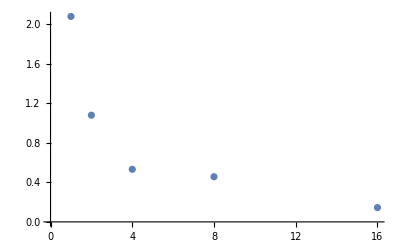

```mathematica
ListPlot[data]
```

```mathematica
f[x_] := {x[[1]],(data[[1]][[2]] )/x[[2]]}

speedup = Map[f, data ]
```

{{1,1.},{2,1.92526},{4,3.90703},{8,4.54984},{16,14.3644}}

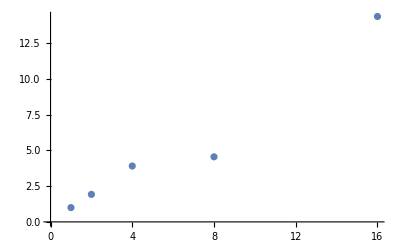

```mathematica
ListPlot[speedup]
```

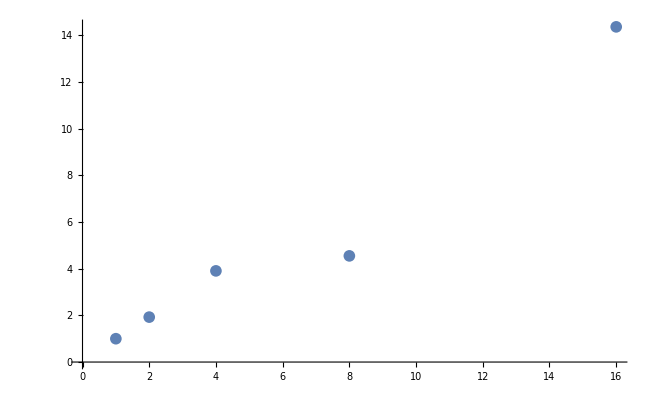

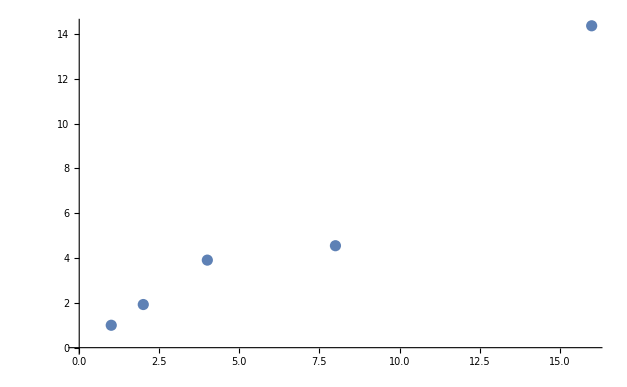

```mathematica
ListPlot[speedup,PlotTheme->"Default"]
```